## Section | Coherent states

The number states have a uniform phase distribution from 0 to 2π, meaning there is not a defined phase. One may think that the classical limit is when the number of photons of a number state goes to infinity , but that is not the case because the average electric field is zero for any n. We seek states such the expectation value of the field operator oscillates sinusoidally. Following this idea, we will introduce the coherent states, that are said to be the “most classical” quantum states of light.  We will explore the properties of the coherent states and its connection to the displacement operator.

#### Key Concepts

Classical-like dynamics

Minimum uncertainty states

Poisson statistics

Displacement operator

### Eigenstates of the annihilation operator and minimum uncertainty

If we consider a superposition of number states that differ in ± 1  |ψ⟩ = c_n|n⟩ + c_(n+1)|n+1⟩, it will have non zero expectation for the electric field operator. More generally, a superposition of all number states will also hold that property. If the annihilation and creation operators, a and a^†, are replaced by complex amplitudes the field can have the structure of a classical field. A reasonable way to try to perform the replacement is to find eigenstates of annihilation operator , in other words solving the eigenvalue equation  where α can be in general complex because the operator is not Hermitian.

We can expand the state |α⟩ in the complete Fock basis:

Replacing in the eigenstate equation and comparing coefficients we get the recurrence relation C_n √n = α C_(n-1) , which is not particularly hard solve and a compact form can be expressed just in function of C_0

Imposing state normalization, we can find C_0 yielding :

This is our first definition of a coherent state in the Fock basis representation

In the Quantum Framework  we can define a not normalized coherent state in a truncated Fock space, and the normalization can be done when needed

Set up the space size, and the annihilation operator:

```mathematica
SetFockSpaceSize[30];
a := AnnihilationOperator[];
```

Not normalized symbolic coherent state:

```mathematica
αket = CoherentState[];
```

See the formula in Dirac notation:

```mathematica
αket//TraditionalForm
```

0+α1+α^2/(√2)2+α^3/(√6)3+α^4/(2 √6)4+α^5/(2 √30)5+α^6/(12 √5)6+α^7/(12 √35)7+α^8/(24 √70)8+α^9/(72 √70)9+α^10/(720 √7)10+α^11/(720 √77)11+α^12/(1440 √231)12+α^13/(1440 √3003)13+α^14/(10080 √858)14+α^15/(30240 √1430)15+α^16/(120960 √1430)16+α^17/(120960 √24310)17+α^18/(725760 √12155)18+α^19/(725760 √230945)19+α^20/(7257600 √46189)20+α^21/(7257600 √969969)21+α^22/(79833600 √176358)22+α^23/(79833600 √4056234)23+α^24/(958003200 √676039)24+α^25/(4790016000 √676039)25+α^26/(62270208000 √104006)26+α^27/(186810624000 √312018)27+α^28/(2615348736000 √44574)28+α^29/(2615348736000 √1292646)29

Normalized coherent state:

```mathematica
coherent := CoherentState[]["Normalize"]
```

Right annihilation operator eigenstate(we compare the amplitudes except the last one because we are using a finite basis):

```mathematica
(a@αket- α αket)["Amplitudes"]//Values //Most
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Define the electric field operator (most general form for a single mode):

```mathematica
Ex:=ⅈ √((h ω)/(2 Subscript[ϵ, 0] V)) (a Exp[ⅈ (k.r-ω t)]-SuperDagger[a] Exp[-ⅈ (k.r-ω t)]);
```

Calculate the mean electric field, for some realization of the value of α:

```mathematica
αrandom=2 Exp[ⅈ Exp[RandomReal[{0,2 π}]]];
```

```mathematica
meanEfield =With[{state=coherent[αrandom]},(SuperDagger[state]@Ex@state)["Scalar"]];
```

Classical expression for electric field in terms of complex amplitudes:

```mathematica
classicalEfield=ⅈ √((h ω)/(2 Subscript[ϵ, 0] V)) (α Exp[ⅈ (k.r-ω t)]-Conjugate[α] Exp[-ⅈ (k.r-ω t)]);
```

Verify the equality:

```mathematica
Chop[meanEfield - (classicalEfield/.α->αrandom)//Simplify]
```

0.+0. ⅈ

Or in polar form, :

```mathematica
FullSimplify[classicalEfield/. α->Abs[α] ⅇ^(ⅈ θ) ,Element[{t,ω,k,θ},Reals]]
```

-√2 Abs[α] √((h ω)/(V ϵ_0)) sin(θ+k.r-t ω)

It can be shown that  so the fluctuations have this form

Expectation value of the electric field squared for a coherent state:

```mathematica
meanEfieldSquared = With[{state=coherent[αrandom]},(SuperDagger[state]@(Ex@Ex)@state)["Scalar"]];
```

Electric field fluctuations:

```mathematica
√Chop[FullSimplify[meanEfieldSquared-meanEfield^2]]
```

0.707107 √((h ω)/(V ϵ_0))

Is one of the expressions that corresponds to the vacuum fluctuations so the coherent state has field mean classical-like values and mean fluctuations of the vacuum

### Coherent state properties

Another check explaining the link to vacuum fluctuations is using the quadrature operators  X_i  from chapter 1, a coherent state  minimizes the uncertainty inequality with both quadrature uncertainties being the same

Load the quadrature operators:

```mathematica
{X1,X2} = QuadratureOperators[];
```

Both quadratures variances equal to 1/4, same as vacuum:

```mathematica
With[{s =αket[αrandom]["Normalize"]},OperatorVariance[s,#]&/@{X1,X2}]//Chop
```

{0.25,0.25}

There is also a relation of α in the phase space context α = ⟨ X_1⟩ + ⅈ ⟨ X_2⟩ obtained from seeking states that saturate the uncertainty inequality. It’s possible to solve an eigenvalue equation given that [X_1,X_2] = ⅈ/2.

Another measurable aspect of the complex amplitude α is related to the photon number operator, it is easy to verify

Number operator:

```mathematica
numberOp := SuperDagger[a]@a;
```

Mean number of photons of a symbolic coherent state:

```mathematica
meanPho=(SuperDagger[CoherentState[]["Normalize"]]@numberOp@CoherentState[]["Normalize"])["Scalar"];
```

Plot the mean number of photons (quadratic in |α|):

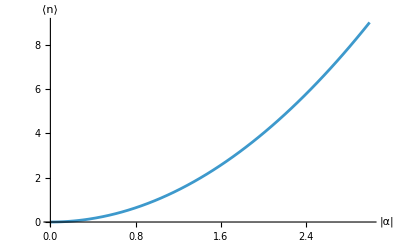

```mathematica
Plot[meanPho,{α,0,3},AxesLabel->{"|α|","⟨n⟩"},LabelStyle->13]
```

Fluctuations of the number operator

```mathematica
fluctuations=√OperatorVariance[CoherentState[]["Normalize"],numberOp];
```

Compare to |α|:

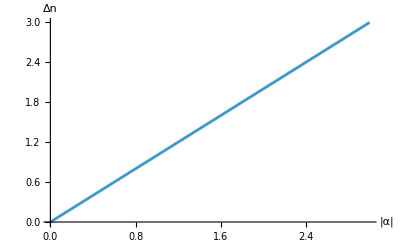

```mathematica
Plot[fluctuations,{α,0,3},AxesLabel->{"|α|","Δn"},LabelStyle->13]
```

This shows that the photon distribution follows a Poisson distribution, this is more clearly shown when calculating P_n  the probability of measuring n photons. From the definition of coherent state in Fock basis it is not difficult to obtain:

The fractional uncertainty  decreases with increasing mean photon number. Also the phase distribution for a coherent state |α⟩ (α = |α| ⅇ^(ⅈ θ)) is:

For large |α| the Poisson distribution approximates to a Gaussian so a compact approximation can be derived

Plot photon distributions, for |α|^2= 1,2,..10:

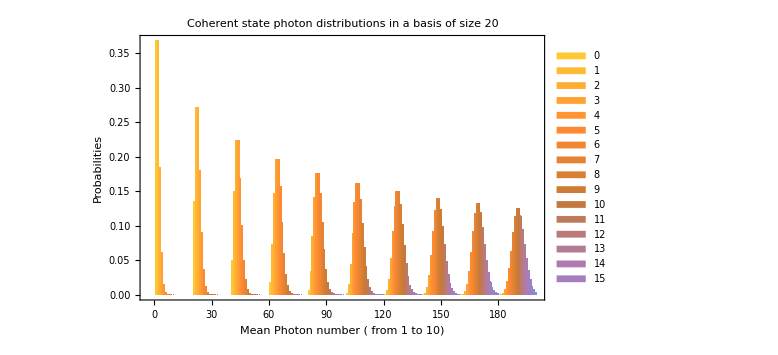

```mathematica
SetFockSpaceSize[20];
BarChart[Table[coherent[√x]["Probabilities"]//Values,{x,1.,10}],]
```

NOTE: Since we are using a truncated basis it is worth noting that to appropriately describe a coherent state with amplitude α, the basis size should be around |α |^2+5 |α| (or higher) to include the tails of the  Poisson distribution

For  example, for  |α| = √10the best size would be 10+5 √10 ≈ 25:

```mathematica
SetFockSpaceSize[25];
```

We can observe the corresponding photon number distribution:

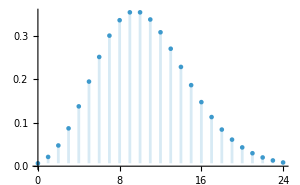

```mathematica
DiscretePlot[Sqrt @ PDF[PoissonDistribution[10],x],{x,0,24},Filling->Bottom,ImageSize->300]
```

“AmplitudesPlot” of the state with the distribution:

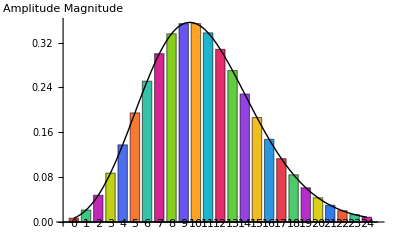

```mathematica
Show[coherent[√10 Exp[ⅈ RandomReal[{0,2π}]]]["AmplitudePlot",LabelStyle->8,ChartLegends->Automatic],,]
```

Plots of phase distributions for different mean photon numbers, becomes more definite when n^— increases:

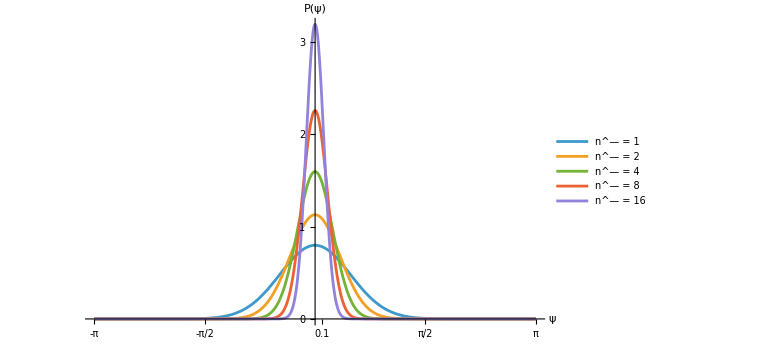

```mathematica
Plot[Evaluate[Table[√((2 Abs[x]^2)/π) Exp[-2 Abs[x]^2 (ψ-Arg[x])^2],{x,{√1,√2,√4,√8,√16}}]],{ψ,-π,π},]
```

So coherent states are quantum states with classical-like  features because:

Mean value of electric field has the form of a classical expression

Electric field fluctuations are those of the vacuum

Fluctuations in the photon number decrease when the mean photon number increases

Their phase becomes more localized when the mean photon number increases

### Displacement operator and displaced vacuum states

There exists an equivalent definition of a coherent state that is based on displacing the vacuum state , it gives more insight why coherent states have must have the uncertainty of the vacuum. The generator is the displacement operator, it is defined as:

And a coherent state can be build as:

Using the disentangling theorem   valid when  but holds

We can check this rearrangement using non-commutative algebra, we just recover the prefactor , because the product of separated terms comes automatically from the Zassenhaus expansion definition:

Load the Zassenhaus function:

```mathematica
zassen =ResourceFunction["ZassenhausTerms"];
```

Define the algebra:

```mathematica
alg =NonCommutativeAlgebra[<|"ScalarVariables"->α|>];
```

Basic commutator:

```mathematica
rels ={a**SuperDagger[a]-SuperDagger[a]**a-1};
```

Perform the calculation using non-commutative algebra functions:

```mathematica
Sum[
NonCommutativePolynomialReduce[
zassen[{α SuperDagger[a],-α*a},n,NonCommutativeMultiply],
rels, {SuperDagger[a],a}, alg ],
{n,2,10}][[-1]]
```

-(α Conjugate[α])/2

In this form we can apply the operator to the vacuum , expanding the first exponential :

Now we note that because the annihilation operator and their powers “kill” the vacuum state except when k =0 , only the vacuum remains. The other exponential can also be expanded

because ,  finally including the normalization constant we see  D(α) |0⟩ is exactly the same as the definition of a coherent state

Verifying symbolically the displacement operator main property , here we are omitting a normalization because quantum state equality works up to a multiplicative global constant:

```mathematica
DisplacementOperator[α][]==CoherentState[][α]
```

True

Using a truncated basis has additional numeric error propagation because [a, a^†] is not exactly the identity. Using a bigger space size or reducing the magnitude of α can control the desired precision.

Pick a value of α:

```mathematica
αrandom = RandomComplex[{2+2ⅈ,3+3ⅈ}];
```

Try with a “small” truncation size:

```mathematica
SetFockSpaceSize[15];
```

We see appreciable numerical error:

```mathematica
(DisplacementOperator[αrandom][]-coherent[αrandom])["Amplitudes"]//Values
```

{-0.000342379,-0.000842463-0.000834373 ⅈ,-0.0000280157-0.00290348 ⅈ,0.00404539-0.00416421 ⅈ,0.0100511-0.000193985 ⅈ,0.0112719+0.0107408 ⅈ,0.000637106+0.0220039 ⅈ,-0.0196752+0.021051 ⅈ,-0.0352543+0.00136131 ⅈ,-0.0300216-0.0275215 ⅈ,-0.00215095-0.0445508 ⅈ,0.0311392-0.0346329 ⅈ,0.0464829-0.00269401 ⅈ,0.0335432+0.0295792 ⅈ,0.00279363+0.0412992 ⅈ}

Use a bigger space size:

```mathematica
SetFockSpaceSize[45];
```

Now the state with this value of α is correctly represented:

```mathematica
(DisplacementOperator[αrandom][]-coherent[αrandom])["Amplitudes"]//Values
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Check the following property  :

```mathematica
DisplacementOperator[α]["Dagger"] == DisplacementOperator[-α]
```

True

From this it is clear  , is a unitary operator

Composing two displacement operators also has the form of a displacement operator times an overall phase factor:

Can be proved using disentangling theorem from the Baker-Campbell-Hausdorff expansion, we see we get the terms of the displacement operator with z = α + β and the phase factor (z - z*)/2 = ⅈ Im(z).

Load the Baker-Campbell-Hausdorff function:

```mathematica
BCH = ResourceFunction["BakerCampbellHausdorffTerms"];
```

Specify the algebra:

```mathematica
alg =NonCommutativeAlgebra["ScalarVariables"->{α,β}];
```

Compute the result:

```mathematica
Sum[NonCommutativePolynomialReduce[
BCH[{α SuperDagger[a]-α*a,β SuperDagger[a]-β*a},n,NonCommutativeMultiply],
rels,
{SuperDagger[a],a},
alg][[-1]],{n,1,7}]
```

(α+β) a^†+a (-Conjugate[α]-Conjugate[β])-(β Conjugate[α])/2+(α Conjugate[β])/2

Intuitively if we do a displacement of α and then a displacement of β, the net displacement is α + β, so we get a coherent state with amplitude α + β:

Pick values of α and β:

```mathematica
SeedRandom[100];
{αrandom,βrandom}= RandomComplex[{-2-2I,2+2I},2]
```

{-1.94852-1.10714 ⅈ,-0.64538+0.777815 ⅈ}

We consider a bigger size because are composing displacements:

```mathematica
SetFockSpaceSize[50];
```

Composition of displacement operators:

```mathematica
composedDisplacement =DisplacementOperator[αrandom]@DisplacementOperator[βrandom][];
```

Result using the coherent |α + β ⟩:

```mathematica
coherentresult =Exp[ⅈ Im[αrandom βrandom*]]coherent[αrandom + βrandom];
```

“AmplitudeList” returns non zero amplitudes, in this case all are zero so the states are the numerically the same:

```mathematica
Chop[composedDisplacement-coherentresult]["AmplitudeList"]
```

{}

### Wave packets and time evolution

The position operator q̂ is defined, such that q̂ |q⟩ = q |q⟩ describes the position eigenstates, in terms of ladder operators can be written as:

```mathematica
SetFockSpaceSize[20];
```

Define the position operator:

```mathematica
q = √(h/(m ω)) QuadratureOperators[][[1]];
```

The Fock states wave functions are the following (derivations can be found in standard quantum mechanics textbooks regarding a quantum harmonic oscillator):

where  ξ=q √(m ω/h) and H_n are Hermite polynomials:

Then the wave function for a coherent state is:

It can be simplified and it takes the form of a gaussian, and the probability distribution |ψ_α(q)|^2 also takes the form of a gaussian

Perform the simplification symbolically:

```mathematica
waveFuncCoh =((m ω)/(π h))^(1/4)ⅇ^(-Abs[α]^2/2)ⅇ^(-ξ^2/2)ⅇ^(ξ^2)FullSimplify[(ⅇ^(-ξ^2) Sum[(z)^n/n!HermiteH[n,ξ],{n,0,∞}])]/.z->α/√2;
```

Show the result:

```mathematica
TraditionalForm[waveFuncCoh]
```

(ⅇ^(-(α/(√2)-ξ)^2-Abs[α]^2/2+ξ^2/2) ((m ω)/h)^(1/4))/π^(1/4)

Plot when α = 1:

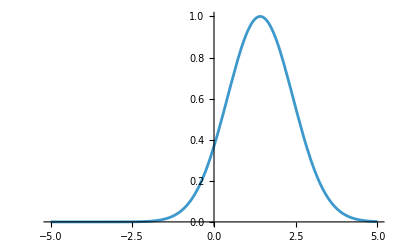

```mathematica
Plot[waveFuncCoh[[1]] /. α->1,{ξ,-5,5}]
```

The diagonal quantum harmonic oscillator Hamiltonian for a single mode field:

```mathematica
H = h ω (SuperDagger[a]@a +1/2 );
```

See the Dirac notation:

```mathematica
H//TraditionalForm
```

(h ω)/2 00+(3 h ω)/2 11+(5 h ω)/2 22+(7 h ω)/2 33+(9 h ω)/2 44+(11 h ω)/2 55+(13 h ω)/2 66+(15 h ω)/2 77+(17 h ω)/2 88+(19 h ω)/2 99+(21 h ω)/2 1010+(23 h ω)/2 1111+(25 h ω)/2 1212+(27 h ω)/2 1313+(29 h ω)/2 1414+(31 h ω)/2 1515+(33 h ω)/2 1616+(35 h ω)/2 1717+(37 h ω)/2 1818+(39 h ω)/2 1919

We create an evolution operator to evolve the states at any time:

```mathematica
QOE=QuantumEvolve[H/h,None,t];
```

A coherent state  remains a coherent state under the evolution , however the complex amplitude phase depends on time  with an extra global phase :

```mathematica
(QOE @ CoherentState[]) == ⅇ^(-ⅈ ω t/2)CoherentState[][α ⅇ^(-ⅈ ω t)]
```

True

The mean value of the position operator for the evolved state behaves like it is a classical oscillator (sinusoidal oscillations). This emphasises another reason why coherent states are called “the most classical” quantum states. This also holds for the mean value of the momentum operator.

Pick a value of α:

```mathematica
αc = RandomComplex[√2{-1-ⅈ,1+ⅈ}];
```

Evolve states:

```mathematica
states=Table[{t,QOE[t][coherent[αc]]},{t,0,10,0.25}];
```

Calculate expectations of position operator:

```mathematica
meanPosition=MapAt[((SuperDagger[#]@q@#)["Scalar"]&),#,2]& /@ states ;
```

Plot the results:

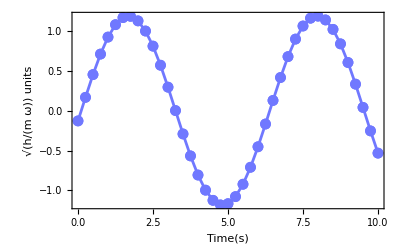

```mathematica
ListLinePlot[Re[meanPosition/.{h->1,m->1,ω->1}],]
```

### Additional properties of coherent states

The  inner  product   of  two  coherent  states | α⟩,  | β ⟩ is:

So when α and β are different clearly the states are not orthogonal , but when the quantity |β - α|^2 is large the states are almost orthogonal ( ⟨ β | α⟩ ≈ 0)

Choose values of α and β:

```mathematica
{αc,βc} = RandomComplex[{1.5+1.5I},2];
```

Compute the bracket:

```mathematica
(coherent[αc]["Dagger"]@coherent[βc])["Scalar"]
```

0.460217+0.0327777 ⅈ

Use the analytical expression:

```mathematica
Exp[-1/2(βc*αc-βc αc*)]Exp[-1/2 Abs[βc-αc]^2]
```

0.460217+0.0327777 ⅈ

The coherent states have a completeness relation  over the complex α plane given by:

We include the exact normalization constant in the case of an infinite basis so we can try to reproduce the theoretical results(here 5 refers to the Fock space size):

```mathematica
Exp[-Abs[α]^2](CoherentState[5]@SuperDagger[CoherentState[5]])
```

ⅇ^(-Abs[α]^2)00+ⅇ^(-Abs[α]^2) Conjugate[α]01+(ⅇ^(-Abs[α]^2) (Conjugate[α])^2)/(√2)02+(ⅇ^(-Abs[α]^2) (Conjugate[α])^3)/(√6)03+(ⅇ^(-Abs[α]^2) (Conjugate[α])^4)/(2 √6)04+α ⅇ^(-Abs[α]^2)10+α ⅇ^(-Abs[α]^2) Conjugate[α]11+(α ⅇ^(-Abs[α]^2) (Conjugate[α])^2)/(√2)12+(α ⅇ^(-Abs[α]^2) (Conjugate[α])^3)/(√6)13+(α ⅇ^(-Abs[α]^2) (Conjugate[α])^4)/(2 √6)14+(α^2 ⅇ^(-Abs[α]^2))/(√2)20+(α^2 ⅇ^(-Abs[α]^2) Conjugate[α])/(√2)21+1/2 α^2 ⅇ^(-Abs[α]^2) (Conjugate[α])^2 22+(α^2 ⅇ^(-Abs[α]^2) (Conjugate[α])^3)/(2 √3)23+(α^2 ⅇ^(-Abs[α]^2) (Conjugate[α])^4)/(4 √3)24+(α^3 ⅇ^(-Abs[α]^2))/(√6)30+(α^3 ⅇ^(-Abs[α]^2) Conjugate[α])/(√6)31+(α^3 ⅇ^(-Abs[α]^2) (Conjugate[α])^2)/(2 √3)32+1/6 α^3 ⅇ^(-Abs[α]^2) (Conjugate[α])^3 33+1/12 α^3 ⅇ^(-Abs[α]^2) (Conjugate[α])^4 34+(α^4 ⅇ^(-Abs[α]^2))/(2 √6)40+(α^4 ⅇ^(-Abs[α]^2) Conjugate[α])/(2 √6)41+(α^4 ⅇ^(-Abs[α]^2) (Conjugate[α])^2)/(4 √3)42+1/12 α^4 ⅇ^(-Abs[α]^2) (Conjugate[α])^3 43+1/24 α^4 ⅇ^(-Abs[α]^2) (Conjugate[α])^4 44

The integrals of the matrix elements in Cartesian coordinates, can be demanding computationally:

```mathematica
Integrate[1/24 α^4 ⅇ^(-Abs[α]^2) Conjugate[α]^4/.α->x+y ⅈ,{x,-∞,∞},{y,-∞,∞}]//AbsoluteTiming
```

{59.1393,π}

```mathematica
Integrate[(α^3 ⅇ^(-Abs[α]^2) Conjugate[α]^2)/(√12)/.α->x+y ⅈ,{x,-∞,∞},{y,-∞,∞}]//AbsoluteTiming
```

{18.4519,0}

The m,n  matrix element of the result is

switching to polar coordinates α = r e^(ⅈ θ), ⅆ^2 α = r ⅆr ⅆθ

We evaluate the integral for general m and n, showing the completeness relation:

```mathematica
Table[{assump,
FullSimplify[
Integrate[Sqrt[1/(m! n!)] r^(m+n+1) Exp[-r^2] Exp[I (m-n) θ],{r,0,∞},{θ,0,2 π},Assumptions->assump],Element[{m,n},Integers]&&n>=0&&m>=0]},
{assump,{m==n,m != n}}] //
TableForm[#,TableHeadings->{None,{"Case", "Result"}}]&
```

Case | Result
m==n | π
m≠n | 0

Corresponding to the matrix of the operator:

```mathematica
Integrate[Normal[r( Exp[-Abs[α]^2](CoherentState[10]@SuperDagger[CoherentState[10]]))["Matrix"]]/. α->r ⅇ^(ⅈ θ),{r,0,∞},{θ,0,2π}]//MatrixForm
```

(π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π)

Any state can be decomposed in terms of coherent states:

When the state is also a coherent state | β ⟩, we see the coherent states are not linear independent and are said to be “overcomplete”, the inner product of the coherent states (exponential factor)  is called a reproducing kernel:

##### Initialization

Load the Quantum Framework:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load the second quantization tools:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Vocabulary

CoherentState |   | defines a non normalized coherent state in
a finite dimensional space
DisplacementOperator |   | single-mode displacement operator in a finite 
dimensional space, coherent state generator

Exercises

What is the behavior of the wave function of a coherent state when it evolves under the Hamiltonian ℏ ω (a^†a+1/2) ? Consider the case with α = 2 and ω = 1 and plot the magnitude and phase, do an animation of the result  (set all other constants to 1).

See wave function at one instant:

AbsArgPlot[waveFuncCoh[[1]]/.α->2 ⅇ^(-2ⅈ 0.6),{ξ,-8,8},Filling->Axis,PlotLegends->Automatic,AxesLabel->{"ξ","|ψ|"}]

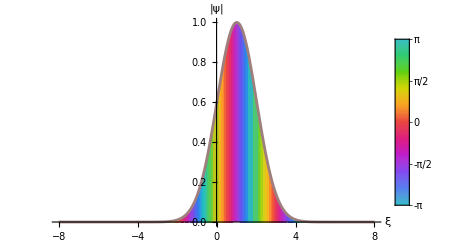

frames =Table[AbsArgPlot[waveFuncCoh[[1]]/.α->2 ⅇ^(-2ⅈ t),{ξ,-8,8},Filling->Axis,PlotLegends->Automatic,AxesLabel->{"ξ","|ψ|"}],{t,0,3,0.05}];

Save GIF locally:

Export[NotebookDirectory[]<>"Coh.GIF",frames,"GIF"];

If we have the unnormalized superposition of coherent states 0.2 |α = 2 ⟩ + 0.5 |β ⟩. What is a possible value of β such there is probability zero of measuring two photons?

Get relevant amplitude

amplitude =(0.2 coherent[2]+0.5 coherent[x+ⅈ y])["Normalize"]["Amplitudes"][[3]];

Minimize the magnitude of the amplitude

result =NMinimize[{Abs[amplitude],-1<=x<=1 &&-1<=y<=1},{x,y}]

{9.40196×10^-12,{x→1.10002×10^-12,y→-0.494693}}

Check visually:

(0.2 coherent[2]+0.5 coherent[x+ⅈ y /. result[[2]]])["Normalize"]["ProbabilityPlot"]

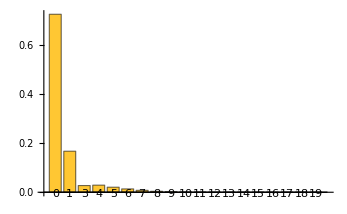

Consider the Kerr non-linear Hamiltonian χ (a^†a)^2. Describe the evolution a coherent state only under this Hamiltonian. Plot the fidelity of the evolved state respect to the initial coherent state. Do you see a periodic behavior? We consider ℏ = 1, use an appropriate value of χ and well a represented coherent state in the chosen truncation size

Kerr non-linearity:

HKerrNonLinear =QuantumOperator[χ(a^†@a)^2,"Parameters"->χ];

Initial coherent state:

ψ0 = coherent[0.6];

Evolved state:

evolved =QuantumEvolve[HKerrNonLinear[4.0],ψ0,{t,0,5}];

Fidelity plot:

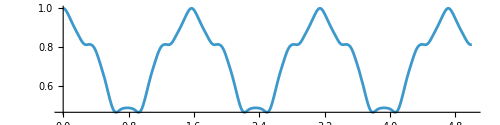

```mathematica
Plot[QuantumSimilarity[ψ0,evolved[t]],{t,0,5},AspectRatio->1/4,ImageSize->500]
```

Changing α and χ vary the form of the curve and the period of the fidelity oscillations